```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/Moat-meanfield/MF_DR/renorm_finitep_v2/specfun/T50/mu250

```mathematica
Re1=Import["./Redata.dat"];
Im1=Import["./Imdata.dat"];
omega=Table[i,{i,1,2001,10}];
ϵ=0.1;
Re2=Re1;
Im2=Table[Im1[[i]][[j]]-2ϵ omega[[j]],{i,1,201},{j,1,201}];
spec=-1/π*Im2/(Re2^2+Im2^2);
Dimensions[Im2]
```

{201,201}

```mathematica
ListPlot3D[spec,PlotRange->{All,All,{0,0.000001}}]
```

-Graphics3D-

```mathematica
special=Clip[spec,{0,0.0000015}];
```

```mathematica
ListPlot3D[special]
```

-Graphics3D-

```mathematica
Export["spec.dat",special]
```

spec.dat

```mathematica
ListPlot3D[Re1]
```

-Graphics3D-

```mathematica
ListPlot3D[-Im1]
```

-Graphics3D-

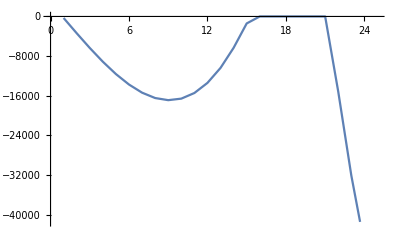

```mathematica
ListLinePlot[Im1[[30]][[1;;25]]]
```